```mathematica
ClearAll["Global`*"];
```

# Flow Control

## Conditionals

#### If

```mathematica
x=17;
If[Mod[x,2]==0,"even","odd"]
```

odd

#### Which

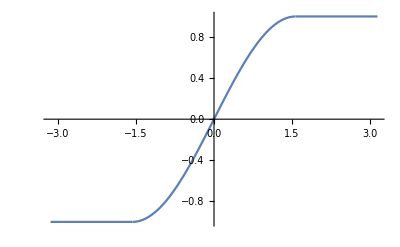

```mathematica
f[x_]:=Which[x<-Pi/2,-1,
-Pi/2<=x<=Pi/2,Sin[x],
x>Pi/2,1
];
Plot[f[x],{x,-Pi, Pi}]
```

#### Switch

```mathematica
x=π;
Switch[x,_Integer,"integer",_,"real"]
```

real

## Loops

#### For

```mathematica
For[x=0,x<=5,x++,Print["- " <> ToString[x]]];
```

- 0

- 1

- 2

- 3

- 4

- 5

#### Do

```mathematica
Do[Print["- " <> ToString[x]],{x,{1,4,9}}]
```

- 1

- 4

- 9

{{1,2,3},{2,4,6},{3,6,9}}

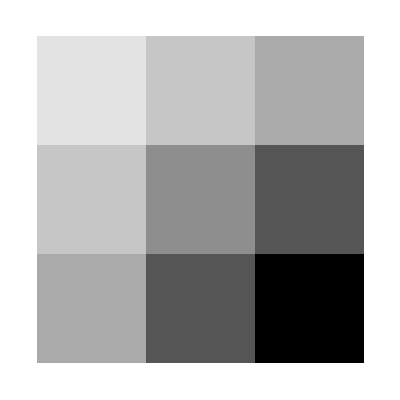

```mathematica
Do[m[i,j]=i j,{i,1,3},{j,1,3}];
A=Array[m,{3,3}]
ArrayPlot[A]
```

#### While

```mathematica
x=0;
While[x <= 5, (
   Print["- " <> ToString[x]];
x++;
 )];
```

- 0

- 1

- 2

- 3

- 4

- 5

#### Nest & NestList

```mathematica
Nest[f,x,4]
```

f[f[f[f[x]]]]

```mathematica
Nest[#^2&,2,4]
```

65536

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

```mathematica
NestList[#^2&,2,4]
```

{2,4,16,256,65536}